```mathematica
(* FLUX *)
```

```mathematica
G=6.67384 10^-8;
MBH=10;
mdot=1;
M=MBH 2 10^33;
MdEdd=MBH 2.23 10^18;
Ledd=1.25 10^38 MBH;
c=30000000000;
Mdot=mdot MdEdd;
Rg=G M/c^2;
Risco=6 Rg;
```

```mathematica
Fss[R_]:=(3 G M Mdot)/(8π R^3)(1-√(Risco/R))
F[R_]:=Fss[R]
```

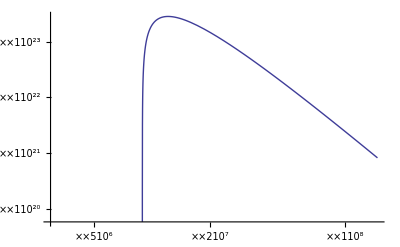

```mathematica
LogLogPlot[F[r],{r,2Rg,100Rg}]
```

```mathematica
NIntegrate[2 2 π R F[R],{R,Risco,Infinity}]
G M Mdot/(2 Risco)
Mdot c^2/ 12
```

1.6725×10^39

1.6725×10^39

1.6725×10^39

```mathematica
(* THICKNESS *)
```

```mathematica
Omk[R_]:=√((G M)/R^3)
κes=0.34;
H[R_]:=(2F[R]κes)/(Omk[R]^2 c)
```

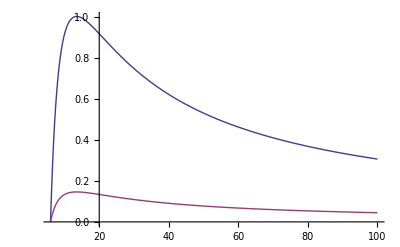

```mathematica
Plot[{H[R Rg]/(R Rg),(5.5 10^4 MBH 16 mdot (1-√(Risco/(R Rg))))/(R Rg)},{R,6,100}]
```

```mathematica
(* RADIAL VELOCITY *)
```

```mathematica
α=0.1;
vr[R_,H_]:=-α (H/R)^2 c/Omk[R](* qualitative *)
vr[R_]:=-7.6 10^8 α (16 mdot)^2 (R/(2 Rg))^(-5/2)(1-√(Risco/(R Rg))) (* blue book,inner region *)
```

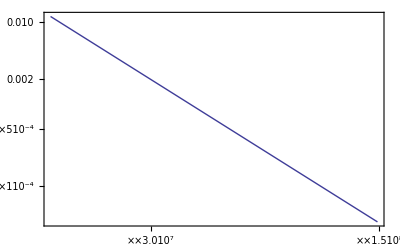

```mathematica
LogLogPlot[-vr[R,H[R]]/c,{R,10 Rg,100Rg},Frame->True]
```

```mathematica
(* SURFACE DENSITY *)
```

```mathematica
Σ[R_]:=Mdot/(-2 π R vr[R])
```

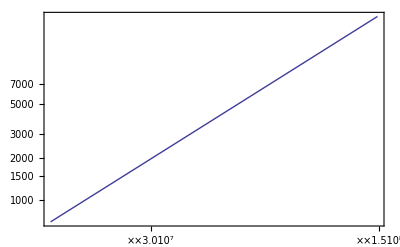

```mathematica
LogLogPlot[Σ[R],{R,10 Rg,100Rg},Frame->True]
```